```mathematica
Trapecios[f_,{a_,b_,n_}]:=Module[{h},
h=(b-a)/n;
N[(f[a]+2*Sum[f[a+k*h],{k,1,n-1}]+f[b])*h/2,20]]
```

```mathematica
CotaTrapecios[a_,b_,n_,M2_]:=N[((b-a)^3*M2)/(12n^2),20]
```

```mathematica
Simpson[f_,{a_,b_,n_}]:=Module[{h},
h=(b-a)/n;
N[(f[a]+4*Sum[f[a+(2*k+1)*h],{k,0,n/2-1}]+2*Sum[f[a+2*k*h],{k,1,n/2-1}]+f[b])*h/3,20] ]
```

```mathematica
CotaSimpson[a_,b_,n_,M4_]:=N[((b-a)^5*M4)/(180n^4),20]
```

```mathematica
G[x_]:=Cos[x]/(x+1)
```

```mathematica
Trapecios[G, {0, 1, 10}]
```

0.60141412919716912939

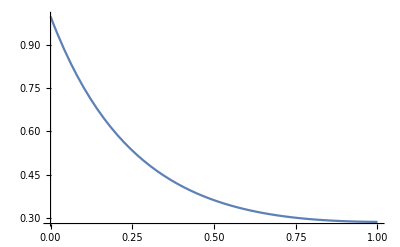

```mathematica
Plot[Abs[G''[x]],{x, 0, 1}, WorkingPrecision->10]
```

```mathematica
CotaTrapecios[0,1,10,1.1]
```

0.000916667

```mathematica
NIntegrate[G[x],{x, 0, 1}, WorkingPrecision->10]
```

0.6010443854

```mathematica
N[%, WorkingPrecision->10]
```

N::precbd: Requested precision WorkingPrecision→10 is not a machine-sized real number between $MinPrecision and $MaxPrecision.

N[N 0.601044[],WorkingPrecision→10]

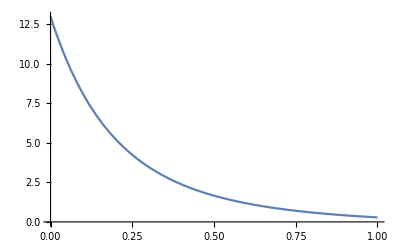

```mathematica
Plot[G''''[x], {x,0,1}]
```

```mathematica
Reduce[CotaSimpson[0,1,n,14]<10^-11, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<-296.97089145035694281||n>296.97089145035694281

```mathematica
Simpson[G, {0,1,298}]
```

0.60104438525642351421

```mathematica
Simpson[f_,{a_,b_,n_}]:=Module[{h},
h=(b-a)/n;
N[(f[a]+4*Sum[f[a+(2*k+1)*h],{k,0,n/2-1}]+2*Sum[f[a+2*k*h],{k,1,n/2-1}]+f[b])*h/3,20] ]
```